```mathematica
c={
{"C3","C4","E4","G4","C5","E5","G5"},(*1^*)
{"A2","A3","C4","E4","A4","C5","E5"},(*6*)
{"F2","F3","A3","C4","F4","A4","C5"},(*4*)
{"G2","G3","B3","D4","G4","B4","D5"}    (*5*)
};
```

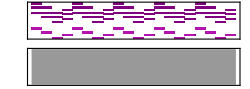

```mathematica
Sound[SoundNote@@@Flatten[Table[Join[
Table[{c⟦n,1⟧,{8s+2(n-1),8s+2n},"Violin"},{n,1,4}],
Flatten[Table[{c⟦n,1;;4⟧,{8s+2(n-1)+(m-1)/2,8s+2(n-1)+m/2}},{n,1,4},{m,1,4}],1]
],{s,0,4}],1]]
```

```mathematica
cs={
{"C4","C5","E5","G5","C6","E6","G6"},(*1^*)
{"A3","A4","C5","E5","A5","C6","E6"},(*6*){"F3","F4","A4","C5","F5","A5","C6"},(*4*){"G3","G4","B4","D5","G5","B5","D6"}    (*5*)
};
```

```mathematica
Gen[num_,st_]:=(g=RealDigits[num,10,16*st]⟦1⟧;
Sound[SoundNote@@@Join[Flatten[Table[Join[
Table[{c⟦n,1⟧,{8s+2(n-1),8s+2n},"Violin"},{n,1,4}],
Flatten[Table[{c⟦n,1;;4⟧,{8s+2(n-1)+(m-1)/2,8s+2(n-1)+m/2}},{n,1,4},{m,1,4}],1]
],{s,0,st-1}],1],
Table[{cs⟦Mod[Ceiling[i/4],4,1],Mod[g⟦i⟧,5]+2⟧,{(i-1)/2,i/2},"Violin"},{i,1,16*st}]
]]
)
```

```mathematica
SetDirectory[NotebookDirectory[]];
Export["pi.mp3",Gen[π,8]]
Export["e.mp3",Gen[E,8]]
Export["sqrt2.mp3",Gen[√2,8]]
```

pi.mp3

e.mp3

sqrt2.mp3